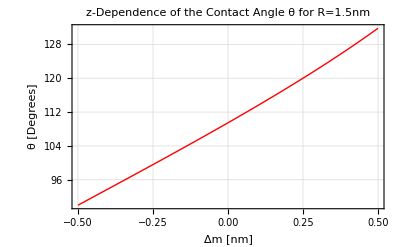

```mathematica
R= 1.5;
m =0.5;
pl15=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=1.5nm", PlotStyle->{Red, Thick}]
```

2.

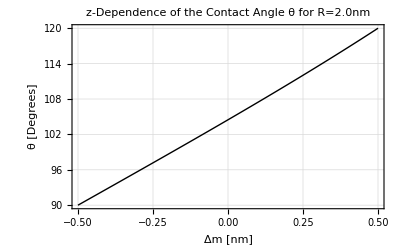

```mathematica
R = 2.0
pl20=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=2.0nm",PlotStyle->{Black,Thick}]
```

2.5

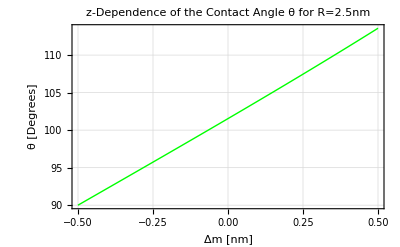

```mathematica
R = 2.5
pl25=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=2.5nm",PlotStyle->{Green,Thick}]
```

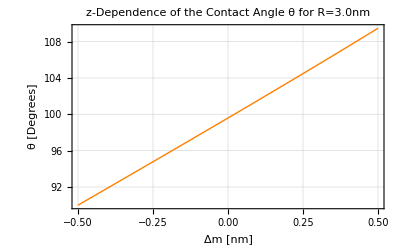

```mathematica
R = 3.0;
pl30=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=3.0nm", PlotStyle->{Orange, Thick}]
```

3.5

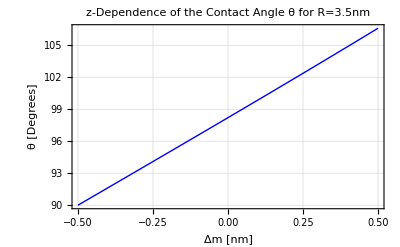

```mathematica
R = 3.5
pl35=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=3.5nm",PlotStyle->{Blue,Thick}]
```

1.

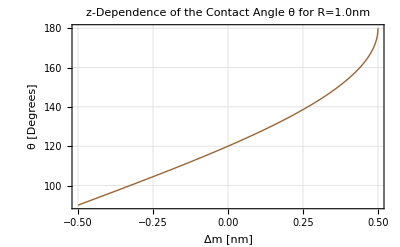

```mathematica
R = 1.0
pl10=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=1.0nm",PlotStyle->{Brown,Thick}]
```

Graphics::gprim: Null was encountered where a Graphics primitive or directive was expected.

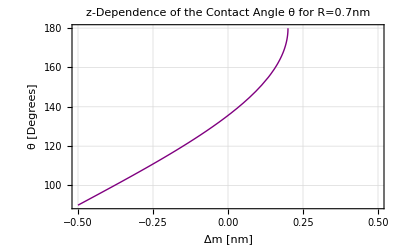

```mathematica
R = 0.7;
pl07=Plot[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)*(180/Pi),{Δm,-0.5, 0.5}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=0.7nm",PlotStyle->{Purple,,Thick}]
```

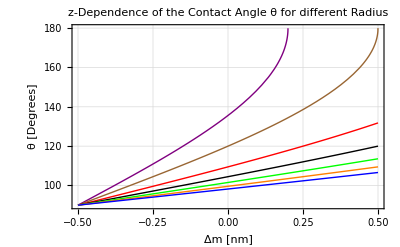

```mathematica
Show[{pl07,pl10,pl15, pl20, pl25, pl30, pl35},PlotLabel->"z-Dependence of the Contact Angle θ for different Radius"]
```

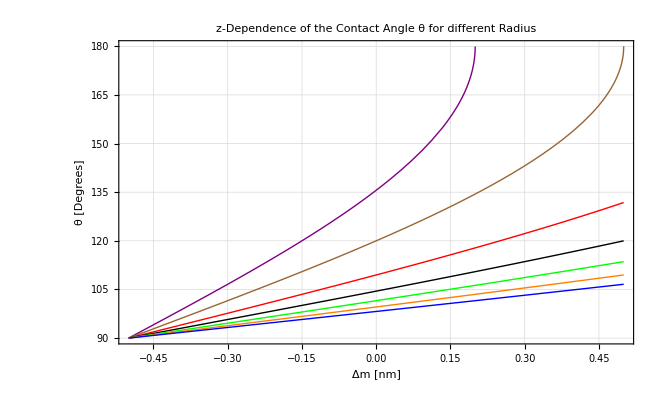

```mathematica
Show[{pl07,pl10,pl15, pl20, pl25, pl30, pl35},PlotLabel->"z-Dependence of the Contact Angle θ for different Radius"] LineLegend[{Directive[Purple,Thick],Directive[ Brown,Thick],Directive[Red,Thick],Directive[Black,Thick],Directive[ Green,Thick],Directive[Orange,Thick],Directive[Blue,Thick]},{"R = 0.7 nm","R = 1.0 nm","R = 1.5 nm","R = 2.0 nm","R = 2.5 nm","R = 3.0 nm","R = 3.5 nm"},LegendFunction->"Frame",LabelStyle->20]
```

84.2608

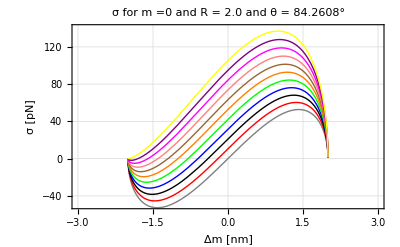

```mathematica
R = 2.0;
costheta=0.1;
m =0.0;
deltaM=10;
theta=ArcCos[costheta]*(180/Pi)
σl1501=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Red, Thick}];
costheta=0.2;
σl1502=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Black, Thick}];
costheta=0.3;
σl1503=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Blue, Thick}];
costheta=0.4;
σl1504=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Green, Thick}];
costheta=0.5;
σl1505=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Orange, Thick}];
costheta=0.6;
σl1506=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Brown, Thick}];
costheta=0.7;
σl1507=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Pink, Thick}];
costheta=0.8;
σl1508=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Magenta, Thick}];
costheta=0.9;
σl1509=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"},PlotStyle->{Purple, Thick}];
costheta=1.0;
σl1510=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Yellow, Thick}];
costheta=0.0;
σl1500=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Gray, Thick}];
Show[σl1500,σl1501,σl1502,σl1503,σl1504,σl1505,σl1506,σl1507,σl1508,σl1509,σl1510,PlotRange->{{-3,3},{-50,140}},PlotLabel->"σ for m =0 and R = 2.0 and θ = "<>ToString[theta]<>"°"]
LineLegend[{Directive[Purple,Thick],Directive[ Brown,Thick],Directive[Red,Thick],Directive[Black,Thick],Directive[ Green,Thick],Directive[Orange,Thick],Directive[Blue,Thick]},{"R = 0.7 nm","R = 1.0 nm","R = 1.5 nm","R = 2.0 nm","R = 2.5 nm","R = 3.0 nm","R = 3.5 nm"},LegendFunction->"Frame",LabelStyle->20]
```

95.7392

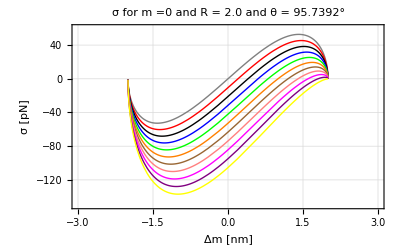

```mathematica
R = 2.0;
costheta=-0.1;
m =0.0;
deltaM=10;
theta=ArcCos[costheta]*(180/Pi)
minσl1501=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Red, Thick}];
costheta=-0.2;
minσl1502=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Black, Thick}];
costheta=-0.3;
minσl1503=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Blue, Thick}];
costheta=-0.4;
minσl1504=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Green, Thick}];
costheta=-0.5;
minσl1505=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Orange, Thick}];
costheta=-0.6;
minσl1506=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Brown, Thick}];
costheta=-0.7;
minσl1507=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Pink, Thick}];
costheta=-0.8;
minσl1508=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Magenta, Thick}];
costheta=-0.9;
minσl1509=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"},PlotStyle->{Purple, Thick}];
costheta=-1.0;
minσl1510=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Yellow, Thick}];
costheta=0.0;
minσl1500=Plot[(Cos[(ArcTan[(m+Δm)/Sqrt[R^2 - (m +Δm)^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m +Δm)^2]*(-52.7),{Δm,-deltaM, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"Δm [nm]","σ [pN]"}, PlotStyle->{Gray, Thick}];
Show[minσl1500,minσl1501,minσl1502,minσl1503,minσl1504,minσl1505,minσl1506,minσl1507,σl1508,σl1509,σl1510,PlotRange->{{-3,3},{-150,60}},PlotLabel->"σ for m =0 and R = 2.0 and θ = "<>ToString[theta]<>"°"]
LineLegend[{Directive[Purple,Thick],Directive[ Brown,Thick],Directive[Red,Thick],Directive[Black,Thick],Directive[ Green,Thick],Directive[Orange,Thick],Directive[Blue,Thick]},{"R = 0.7 nm","R = 1.0 nm","R = 1.5 nm","R = 2.0 nm","R = 2.5 nm","R = 3.0 nm","R = 3.5 nm"},LegendFunction->"Frame",LabelStyle->20]
```